Mathematica code  for SHO based off of Dr. Tate’s “Shooting Method” used in class 1/10/18	John Waczak

```mathematica
SetOptions[Plot,PlotStyle->{Blue,AbsoluteThickness[2], Dashed},
ImageSize->500,AxesStyle->Directive[FontFamily->"Arial",FontSize->18,Black,AbsoluteThickness[0.5],Arrowheads[0.04]]];
```

```mathematica
m = 1
ω = 1
ℏ= 1
```

1

1

1

```mathematica
v[x_]:= (1/2)*m*ω^2*x^2;
```

Here we graph the harmonic potential

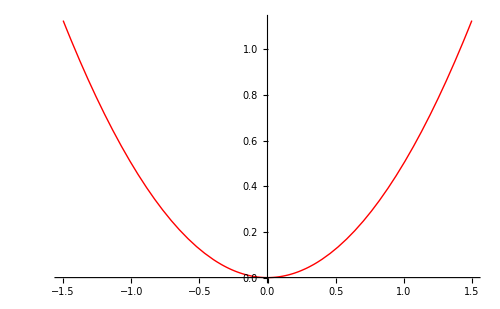

```mathematica
Plot[v[x],{x,-1.5,1.5},PlotStyle->{Red,AbsoluteThickness[1]}]
```

Now we choose an energy of 0.5 (because we have sent m, ω, and ℏ to 1 we expect the ground state 
to have an energy of ℏω(n + 1/2) with n =0)

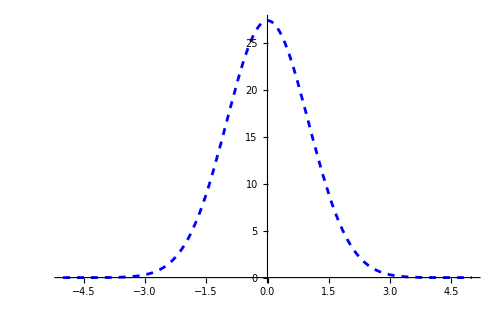

```mathematica
energy= 0.5;
xMax=5;
solution=NDSolve[{psi''[x]==-2(energy-v[x])psi[x],psi[-xMax]==0,psi'[-xMax]==0.001},psi,{x,-xMax,xMax}];
Plot[psi[x]/.solution,{x,-xMax,xMax}]
```

Now we find the second eigenstate to have an energy of 1.5 in our units

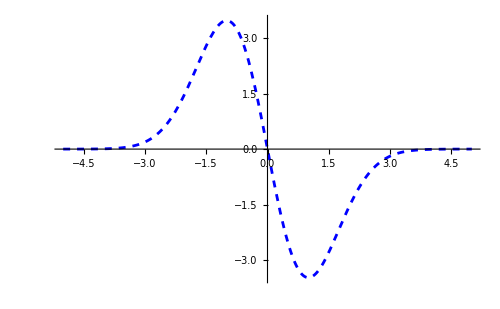

```mathematica
energy= 1.5;
xMax=5;
solution=NDSolve[{psi''[x]==-2(energy-v[x])psi[x],psi[-xMax]==0,psi'[-xMax]==0.001},psi,{x,-xMax,xMax}];
Plot[psi[x]/.solution,{x,-xMax,xMax}]
```

Now, going back to the ground state, we can see how sensitive the system is as 
an increase of one ten thousandth was enough make the solution blow up 
to infinity.

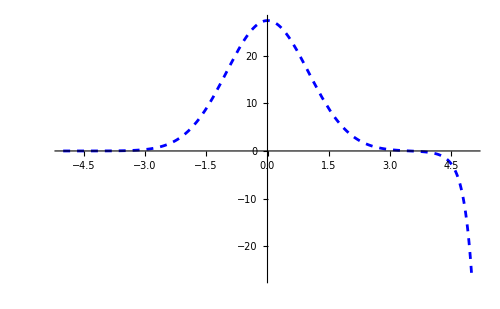

```mathematica
energy= 0.50001;
xMax=5;
solution=NDSolve[{psi''[x]==-2(energy-v[x])psi[x],psi[-xMax]==0,psi'[-xMax]==0.001},psi,{x,-xMax,xMax}];
Plot[psi[x]/.solution,{x,-xMax,xMax}]
```